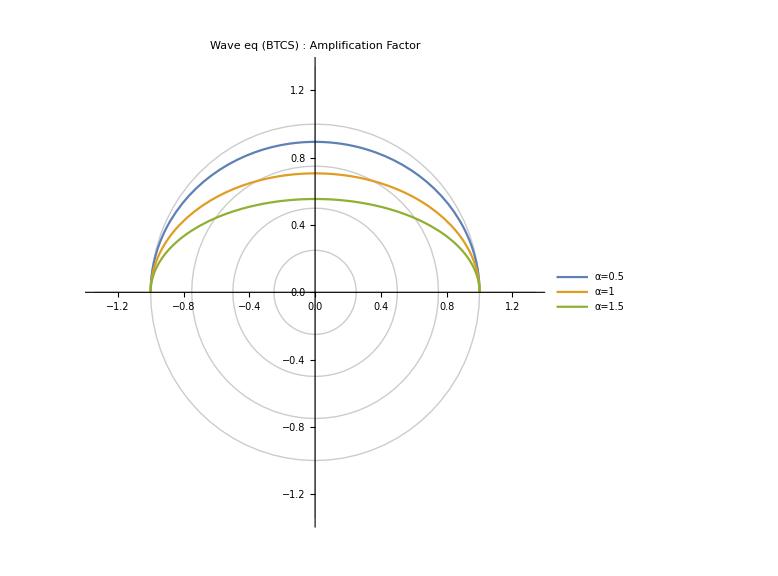

```mathematica
With[{alpha1=0.5, alpha2=1, alpha3=1.5},PolarPlot[{1/Sqrt[1+alpha1^2*Sin[p]^2],1/Sqrt[ 1+alpha2^2*Sin[p]^2],1/Sqrt[1+alpha3^2*Sin[p]^2]}, {p,0,Pi}, PlotStyle->Thick, AxesLabel->{Style["|G/G_e|", Black,Medium]}, PlotLegends->{"α=0.5","α=1","α=1.5"}, PlotLabel->Style[ "Wave eq (BTCS) : Amplification Factor", Black, Medium], PolarGridLines->{{0,Pi/2,Pi,3 Pi/2},{0.25,0.5,0.75,1}},PolarTicks->{"Radians", Automatic},ImageSize->Large]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

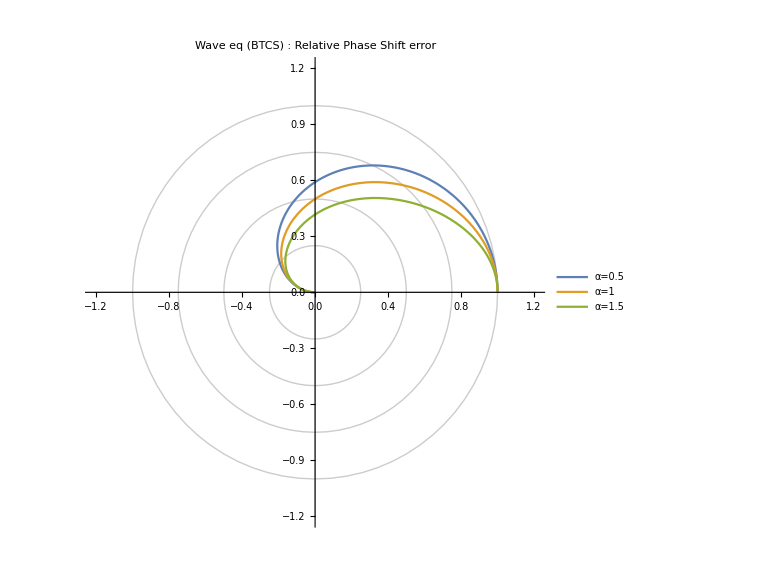

```mathematica
With[{nu1=0.5, nu2=1, nu3=1.5},PolarPlot[{ArcTan[-nu1*Sin[th]]/(-nu1*th), ArcTan[-nu2*Sin[th]]/(-nu2*th), ArcTan[-nu3*Sin[th]]/(-nu3*th)},{th, 0, Pi},PlotStyle->Thick, AxesLabel->{Style["ϕ/ϕ_e",Black, Medium]}, PlotLegends->{"α=0.5","α=1","α=1.5"}, PlotLabel->Style["Wave eq (BTCS) : Relative Phase Shift error", Black, Medium], PolarTicks->{{0,Pi/4,Pi/2,(3 Pi)/4,Pi,(5 Pi)/4,(3 Pi)/2,(7 Pi)/4},{0,.2,.4,.6,.8,1}},PolarGridLines->{{0,Pi/2,Pi,3 Pi/2},{0.25,0.5,0.75,1}},ImageSize->Large]]
```

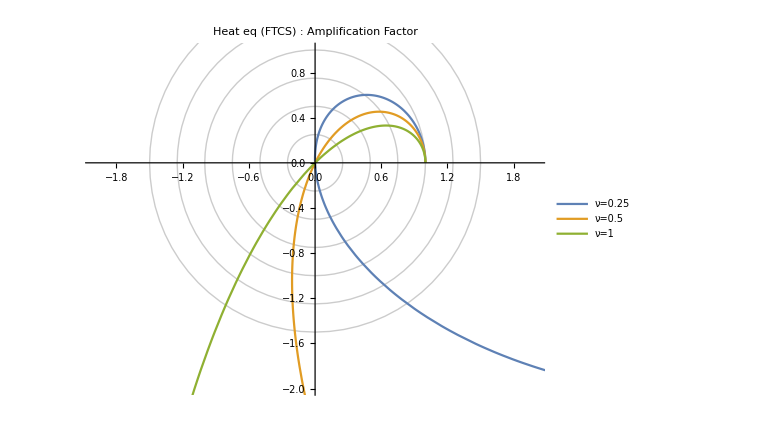

```mathematica
With[{mu1=0.25, mu2=0.5, mu3=1}, PolarPlot[{1-4*mu1*Sin[x/2]^2/Exp[-mu1*x^2], 1-4*mu2*Sin[x/2]^2/Exp[-mu2*x^2], 1-4*mu3*Sin[x/2]^2/Exp[-mu3*x^2]}, {x,0,Pi},PlotRange->{{-2,2},{-2,1} },PlotLegends->{"ν=0.25", "ν=0.5", "ν=1"}, PlotStyle->Thick, AxesLabel->{Style["|G/G_e|", Black,Medium]}, PlotLabel->Style[ "Heat eq (FTCS) : Amplification Factor", Black, Medium],PolarGridLines->{{0,Pi/2,Pi,3 Pi/2},{0.25,0.5,0.75,1,1.25,1.5}},PolarTicks->{"Radians", Automatic},ImageSize->Large]]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

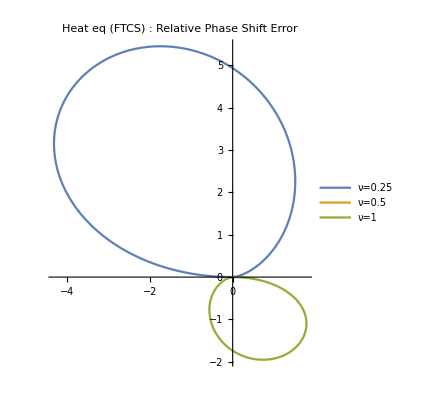

```mathematica
With[{mu1=0.25, mu2=0.5, mu3=1}, PolarPlot[{ArcTan[-2*mu1*Sin[x]/(1-2*mu1)]/-mu1*x,ArcTan[-2*mu2*Sin[x]/(1-2*mu2)]/-mu2*x,ArcTan[-2*mu3*Sin[x]/(1-2*mu3)]/-mu3*x }, {x,0,Pi}, PlotLegends->{"ν=0.25", "ν=0.5", "ν=1"},PlotStyle->Thick, AxesLabel->{Style["ϕ/ϕ_e",Black, Medium]},  PlotLabel->Style[ "Heat eq (FTCS) : Relative Phase Shift Error", Black, Medium]]]
```

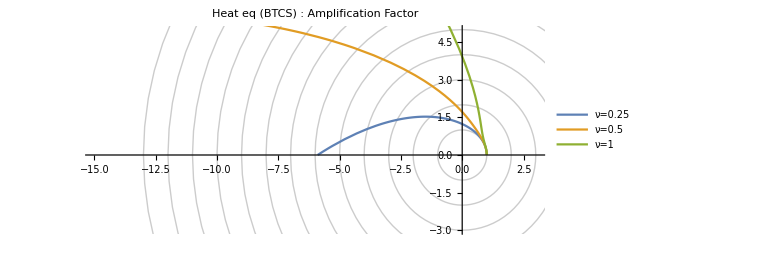

```mathematica
With[{mu1=0.25, mu2=0.5, mu3=1}, PolarPlot[{Exp[mu1*x^2]/(1+4*mu1*Sin[x/2]^2),Exp[mu2*x^2]/( 1+4*mu2*Sin[x/2]^2),Exp[mu3*x^2]/( 1+4*mu3*Sin[x/2]^2)}, {x,0,Pi}, PlotRange->{{-15,3},{-3,5}},PlotLegends->{"ν=0.25", "ν=0.5", "ν=1"}, PlotStyle->Thick, AxesLabel->{Style["|G/G_e|", Black,Medium]}, PlotLabel->Style[ "Heat eq (BTCS) : Amplification Factor", Black, Medium], PolarGridLines->{{0,Pi/2,Pi,3 Pi/2},{1,2,3,4,5,6,7,8,9,10,11,12,13}},ImageSize->Large]]
```